```mathematica
(*RegionPlot3D[x^2+y^2<z^2,{x,-1,1},{y,-1,1},{z,0,1},
ColorFunction->"Rainbow" ]*)
(*SetDirectory["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\mathematica\\misc"]*)
(*shape = Import[ "filledShape1.png" ]*)
(*data[[400]][[400]]
data[[4]][[4]]*)
(*data[[RandomInteger[1, dd[[1]]]]][[RandomInteger[1, dd[[2]]]]][[1]]*)
(*data[[200]]*)
```

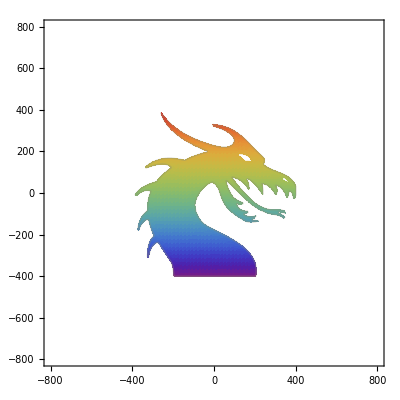

```mathematica
data = ColorConvert[ (*shape*)-Graphics- , "Grayscale" ] // ImageData  ;
dd = data // Dimensions ;

ClearAll[checkAgainstRange] ;
checkAgainstRange::usage = "This is to deal with InputForm Manipulators, that allow non-numeric values to be passed, or values that exceed the range specified in the Manipulator." ;
checkAgainstRange[v_,default_,lowerLimit_, upperLimit_, typeFunc_ : NumberQ] := 
Module[{result},
result = If [ typeFunc[v],v, default] ;

result = If [ result <= upperLimit, result,default ] ;
result = If [ result >= lowerLimit, result,default ] ;

result
] ;

ClearAll[f]
f[point_List] := Module[{m, dr, scaled, r, s, sc},
dr = Take[ dd, 2] ;
scaled = Floor[ {{0, -1},{1, 0}}. point  + (dr + {1,1}) /2] ;
{r, s} = checkAgainstRange[scaled[[#]], 1, 1, dr[[#]]] &/@ Range[2];

(data[[r]][[s]][[2]] == 1)
]

ClearAll[ followPointWithinConeToTop]
followPointWithinConeToTop::usage = "For a set of coordinates, point = {x, y, z}, follow the point {x,y} in the plane at height z to a height of h (either on the interior or the exterior of a cone)" ;
followPointWithinConeToTop[point_List, h_] := Module[{planeProj, z},
planeProj = Take[point, 2] ;
z = point // Last ;

h planeProj / z
]

(*RegionPlot[ f[{x, y}, #], {x, -1, 1}, {y, -1,1}, PlotRange -> Full ] &/@ {0.5, 1, 2, 4, 8}*)

RegionPlot[ f[{x, y}], {x, -dd[[1]], dd[[1]]}, {y, -dd[[2]],dd[[2]]}
(*, PlotRange -> Full*)
, PerformanceGoal -> "Quality"
, PlotPoints -> 90
, ColorFunction->"Rainbow" ]
```

```mathematica
(*2^(#-2) &/@ Range[5]*)
```

```mathematica
(*RegionPlot3D[ f[{x, y}, 2^(z-2)], {x, -1, 1}, {y, -1,1}, {z, 1, 5}, PlotRange -> Full ] *)
```

```mathematica
RegionPlot3D[ f[followPointWithinConeToTop[{x, y, z}, 1]], {x, -dd[[1]], dd[[1]]}, {y, -dd[[2]],dd[[2]]}, {z, 0.001, 1}
, PerformanceGoal -> "Quality"
, PlotPoints -> 90
, ColorFunction->"Rainbow" 
 ]
```